### Set-up (metric and equations of motion)

#### Kerr metric

```mathematica
Σ[r_,θ_,a_]:=r^2+a^2 Cos[θ]^2;
Δ[r_,a_]:=r^2-2r+a^2;
```

```mathematica
coord={tt,rr,θθ,ϕϕ};
metric=Simplify@({{-(1-(2rr)/Σ[rr,θθ,aa]), 0, 0, -(2rr aa Sin[θθ]^2)/Σ[rr,θθ,aa]}, {0, Σ[rr,θθ,aa]/Δ[rr,aa], 0, 0}, {0, 0, Σ[rr,θθ,aa], 0}, {-(2rr aa Sin[θθ]^2)/Σ[rr,θθ,aa], 0, 0, (rr^2+aa^2+(2rr aa^2)/Σ[rr,θθ,aa] Sin[θθ]^2)Sin[θθ]^2}});
$Assumptions=And[rr>2,-1<aa<1,0<θθ<π,0<ϕϕ<2π];
metricsign=-1;
<<Diffgeo`
```

```mathematica
zeroQ@Einstein
```

True

#### Equations of motion

```mathematica
dtdλ[r_,θ_,a_,e_,Lz_,Q_]:=(-a^2 e Sin[θ]^2+a Lz+(r^2+a^2)/Δ[r,a] P[r,a,e,Lz])/Σ[r,θ,a];
drdλ[r_,θ_,a_,e_,Lz_,Q_,signr_]:=signr (√R[r,a,e,Lz,Q])/Σ[r,θ,a];
dθdλ[r_,θ_,a_,e_,Lz_,Q_,signθ_]:=signθ (√Θ[θ,a,e,Lz,Q])/Σ[r,θ,a];
dϕdλ[r_,θ_,a_,e_,Lz_,Q_]:=(-a e+Lz Csc[θ]^2+a/Δ[r,a] P[r,a,e,Lz])/Σ[r,θ,a];
```

```mathematica
P[r_,a_,e_,Lz_]:=e(r^2+a^2)-a Lz;
Θ[θ_,a_,e_,Lz_,Q_]:=Q+Cos[θ]^2(a^2 e^2-Lz^2 Csc[θ]^2);
R[r_,a_,e_,Lz_,Q_]:=P[r,a,e,Lz]^2-Δ[r,a]((a e-Lz)^2+Q);
```

#### Change of coordinates

```mathematica
dvdλ[r_,θ_,a_,e_,Lz_,Q_,signr_]:=dtdλ[r,θ,a,e,Lz,Q]+(r^2+a^2)/Δ[r,a] drdλ[r,θ,a,e,Lz,Q,signr];
dφdλ[r_,θ_,a_,e_,Lz_,Q_,signr_]:=dϕdλ[r,θ,a,e,Lz,Q]+a/Δ[r,a] drdλ[r,θ,a,e,Lz,Q,signr];
```

```mathematica
T[r_,a_]:=r+1/2 Log[Δ[r,a]^2/16]+1/(2 √(1-a^2))Log[((r-1-√(1-a^2))/(r-1+√(1-a^2)))^2];
Φ[r_,a_]:=a/(4 √(1-a^2))Log[((r-1-√(1-a^2))/(r-1+√(1-a^2)))^2];
And[D[T[r,aa], r]==(r^2+aa^2)/Δ[r,aa],D[Φ[r,aa], r]==aa/Δ[r,aa]]//Simplify
```

True

### Images

The ‘camera’ points radially with an array of ‘pixels’ a distance Δr from the focus with size Δx × Δy (think pinhole camera). For each pixel the constants e,L_z,Q are found for the geodesic passing from that pixel to the focus. The geodesic equations are integrated until some stopping condition is met.

#### E,L_z,Q for given initial conditions

```mathematica
Spherical[x_,y_,z_,r_,α_,β_,γ_,δ_]:=ToSphericalCoordinates[
RotationMatrix[β,{1,0,0}].RotationMatrix[α,{0,0,1}].
(RotationMatrix[δ,{0,1,0}].RotationMatrix[γ,{0,0,1}].{x,y,z}+{0,0,r})
];
```

```mathematica
GetxyeLzQarray[a_,rcam_,Δr_,Δx_,Δy_,xres_,yres_,α_,β_,γ_,δ_]:=Module[{focus,pixels,x,y,i,j,xyeLzQ},
focus=Spherical[0,0,0,rcam,α,β,0,0];
pixels=Table[{x,y,focus-Spherical[x,y,Δr,rcam,α,β,γ,δ]},{y,-Δy,Δy,(2Δy)/(yres-1)},{x,-Δx,Δx,(2Δx)/(xres-1)}];
xyeLzQ=Table[{
pixels[[i,j,1]],
pixels[[i,j,2]],
{Sign[pixels[[i,j,3,1]]],Sign[pixels[[i,j,3,2]]]},
{e,Lz,Q}/.First@NSolve[{pixels[[i,j,3]]=={
drdλ[rcam,β,a,e,Lz,Q,Sign[pixels[[i,j,3,1]]]],
dθdλ[rcam,β,a,e,Lz,Q,Sign[pixels[[i,j,3,2]]]],
dϕdλ[rcam,β,a,e,Lz,Q]
},e>0},{e,Lz,Q}]
},{i,yres},{j,xres}];
Return[xyeLzQ];
];
```

#### Integration

```mathematica
GetNullGeodesic[t0_,r0_,θ0_,ϕ0_,a_,eLzQ_,signs_,λmax_,rin_,rout_]:=
Module[{v0=t0+T[r0,a],φ0=ϕ0+Φ[r0,a],e=eLzQ[[1]],Lz=eLzQ[[2]],Q=eLzQ[[3]],eqns,init,soln,crossings},
eqns=Simplify@{
v'[λ]==Re@dvdλ[r[λ],θ[λ],a,e,Lz,Q,signr[λ]],
r'[λ]==Re@drdλ[r[λ],θ[λ],a,e,Lz,Q,signr[λ]],
θ'[λ]==Re@dθdλ[r[λ],θ[λ],a,e,Lz,Q,signθ[λ]],
φ'[λ]==Re@dφdλ[r[λ],θ[λ],a,e,Lz,Q,signr[λ]]
};
init={v[0]==v0,r[0]==r0,θ[0]==θ0,φ[0]==φ0,signr[0]==signs[[1]],signθ[0]==signs[[2]]};

crossings={};

soln=First@NDSolve[{eqns,init,
WhenEvent[r[λ]≤1,"StopIntegration"],
WhenEvent[r[λ]≥1.5r0,"StopIntegration"],
WhenEvent[θ[λ]==π/2&&rin≤r[λ]≤rout,AppendTo[crossings,λ]],
WhenEvent[θ[λ]<0.001,{signθ[λ]->-signθ[λ],φ[λ]->φ[λ]+π}],
WhenEvent[θ[λ]>π-0.001,{signθ[λ]->-signθ[λ],φ[λ]->φ[λ]+π}],
WhenEvent[R[r[λ],a,e,Lz,Q]<0.001,{r[λ]->r[λ]-signr[λ]0.001,signr[λ]->-signr[λ]}],
WhenEvent[Θ[θ[λ],a,e,Lz,Q]<0.00000001,{θ[λ]->θ[λ]-signθ[λ]0.00000001,signθ[λ]->-signθ[λ]}]
},
{v,r,θ,φ,signr,signθ},{λ,0,λmax},DiscreteVariables->{signr,signθ}];
Return[{soln,crossings}];
];
```

```mathematica
GetNullTraj[soln_,adj_]:=Module[{λm,x,y,z},
λm=(r/.soln)["Domain"][[1,2]];
x=r[λ λm]Sin[θ[λ λm]]Cos[φ[λ λm]-adj Φ[r[λ λm]]];
y=r[λ λm]Sin[θ[λ λm]]Sin[φ[λ λm]-adj Φ[r[λ λm]]];
z=r[λ λm]Cos[θ[λ λm]];
Return[{x,y,z}/.soln];
];
```

#### Redshift

Would like to understand the redshift (blueshift) between the source and detector (camera). The energy of a photon is measured by

ω=-u^μ p_μ

for observer 4-velocity u^μ. Let’s suppose that the source is in some (stable) equitorial, circular orbit and that the detector is at some fixed r,θ,ϕ so that ω_detector==-u^t p_t. One can show that the time-like geodesic equations in the equitorial plane for fixed r determines u^μ entirely (recall that a^2≤M^2):

u^t==-(r^(3/2)±a √M)/(√(r^2(r-3M)±2a √M r^(3/2))), u^ϕ==∓(√M)/(√(r^2(r-3M)±2a √M r^(3/2)))

The two signs are for co- and counter-rotating. Notice that

dϕ/dt==u^ϕ/u^t==±(√M)/(r^(3/2)±a √M)

which reduces to Kepler’s 3^d law for a==0. From the form of u^t,u^ϕ we can identify the minimal r for which a circular orbit exists:

r(r-3M)^2-4M a^2==0

This is at least M at most 4M, changing as a ranges in -M≤a≤M.

Recall that p^μ==dx^μ/dλ for the null geodesic, with λ free to be rescaled. We can compute ω_detect/ω_source unambiguously, however.

ω_source==[-g_tt u_source^t p^t-g_tϕ(u_source^t p^ϕ+u_source^ϕ p^t)-g_ϕϕ u_source^ϕ p^ϕ]_(x^μ==source)
ω_detect==[-g_tt u_detect^t p^t]_(x^μ==detect)

```mathematica
RedShift[geo_,λ_]:=Module[{ωs,ωd},
ωs=((√r[λ](r[λ]-2)+a)(v'[λ]-(r[λ]^2+a^2)/Δ[r[λ],a] r'[λ])-(r[λ]^2-2a √r[λ]+a^2)(φ'[λ]-a/Δ[r[λ],a] r'[λ]))/(√(r[λ]^2(r[λ]-3)+2a r[λ]^(3/2)))/.geo;
ωd=((r[0]-2)(r[0]^(3/2)+a)(v'[0]-(r[0]^2+a^2)/Δ[r[0],a] r'[0]))/(r[0] √(r[0]^2(r[0]-3)+2a r[0]^(3/2)))/.geo;
Return[ωd/ωs];
];
```

```mathematica
f[r_]:=(1-rin/r)(rout^2/r^2-1)(27 rin^2 rout)/(6 rin^2 (-3 rout+√(3 rin^2+rout^2))+2 rout^2 (rout+√(3 rin^2+rout^2)));
```

#### Image

```mathematica
ColorPixel[soln_,T0_,redshiftQ_,lum_]:=Module[{geo,stopCond,λs,colors,radii,opac},
geo=soln[[1]];
λs=soln[[2]];

If[Length@λs==0,Return[Black]];

colors=Table[ColorData["BlackBodySpectrum"][T0 RedShift[geo,λ]],{λ,λs}];
opac=Table[f[r[λ]/.geo],{λ,λs}];

If[Length@opac==2,
opac[[2]]=(1-opac[[1]]^0.25)opac[[2]];
];

AppendTo[colors,Black];
AppendTo[opac,1-Total@opac];

color=Blend[colors,opac];
Return[color]

];
```

```mathematica
a=0.9;        (* BH spin parameter *)
r0=50;        (* Camera radial position *)
{α,β}={0,π/2.4};        (* Angular position of camera *)
{γ,δ}={0,0};        (* Angular direction of camera *)
{Δr,Δx,Δy}={0.1,0.035,0.02};        (* Dimensions of camera *)
{xres,yres}={35,20};        (* Resolution *)
{rin,rout}={4,15};         (* Inner and outer radii of disk *)
λmax=1700;        (* Maximum affine parameter for integration *)
```

```mathematica
(* Get array of pixel (relative) positions and corresponding constants of motion *)
Print["Getting "<>ToString[xres yres]<>" conserved quantities for "<>ToString[xres]<>"×"<>ToString[yres]<>" image..."]
xyeLzQArray=GetxyeLzQarray[a,r0,Δr,Δx,Δy,xres,yres,α,β,γ,δ];
xyArray=xyeLzQArray[[All,All,{1,2}]];
eLzQArray=xyeLzQArray[[All,All,{3,4}]];

tStart=TimeObject[];

(* Integrate for each null geodesic *)
Monitor[
nullGeodesics=Table[GetNullGeodesic[0,r0,β,0,a,eLzQArray[[i,j,2]],eLzQArray[[i,j,1]],λmax,rin,rout],{i,yres},{j,xres}];,
Column@{
ProgressIndicator[xres(i-1)+j,{1,xres yres}],
"Elapsed time:   \t"<>ToString[TimeObject[]-tStart],
"Est. time to go:\t"<>ToString[(TimeObject[]-tStart)((xres yres)/(xres(i-1)+j)-1)]
}
]; 
Print["Time: ",ToString[TimeObject[]-tStart]]
Print["Max λ: ",Max[(r["Domain"]/.Flatten[nullGeodesics,1][[All,1]])[[All,1,2]]]]
```

Getting 700 conserved quantities for 35×20 image...

Time: 6.47244 minutes

Max λ: 1329.19

```mathematica
T0=4500;
includeRedshift=True;
includeLum=True;
image=Table[ColorPixel[nullGeodesics[[i,j]],T0,includeRedshift,includeLum],{i,yres},{j,xres}];
```

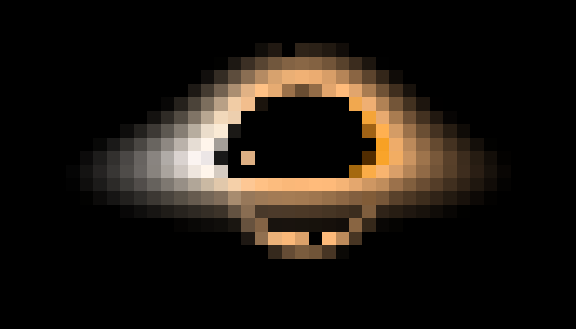

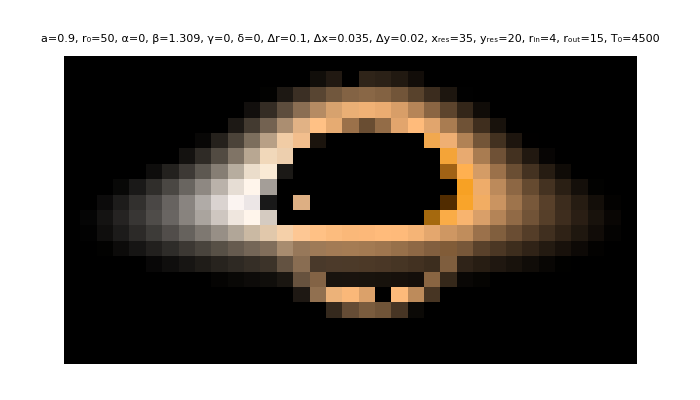

```mathematica
blur=60;
ArrayPlot[image,AspectRatio->Δy/Δx,Frame->False,PlotRangePadding->None,Background->Black,ColorFunctionScaling->False,ImageSize->Large]
Show[
GaussianFilter[%,blur,Padding->Black],
ImageSize->700,
PlotLabel->Style[StringJoin@{
"a=",ToString[a],", ",
"r_0=",ToString[r0],", ",
"α=",ToString[α],", ",
"β=",ToString[β],", ",
"γ=",ToString[γ],", ",
"δ=",ToString[δ],", ",
"Δr=",ToString[Δr],", ",
"Δx=",ToString[Δx],", ",
"Δy=",ToString[Δy],", ",
"x_res=",ToString[xres],", ",
"y_res=",ToString[yres],", ",
"r_in=",ToString[rin],", ",
"r_out=",ToString[rout],", ",
"T_0=",ToString[T0]
},Black]
]
```

```mathematica
(*Export["GitHub/BH-raytracing/images/ex1.png",%,ImageSize->1000]*)
```

GitHub/BH-raytracing/images/ex1.png